# RQA Exploration

Alison Ord

Flip Phillips

## To do notes

7 July 2019
• Plot the numbers against the value of the timeseries - and modify the existing plots so that the x axis represents the absolute position within the timeseries, not just the position within the epoch
• Work out how to interrogate a particular RQA while moving through the data - 12 little recurrence plots look very pretty - but how about when you interrogate 120,000 points, 260,000 points, 1 trillion points?

## Initialise

Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

```mathematica
(* <<RQA` *)
```

The package is built on the equations expressed in Webber and Marwan (2015).

## Find and load the data

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]];
```

```mathematica
(* data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","r30datab.dat"}]]] ; *)
```

data=Flatten[Import["C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\Rule30Results\r30datab.dat"]]

We start by using the data from the same folded rock, or to Rule30, to which we applied the nonlinear tools of spatial attractor, wavelet transform (2D and 3D), Hurst exponents, singularity spectrum (not yet in mtca), and so on.

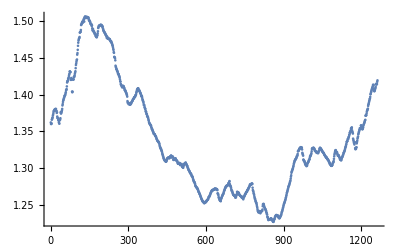

```mathematica
ListPlot[data]
```

We create a time series in the form required by mtca.

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

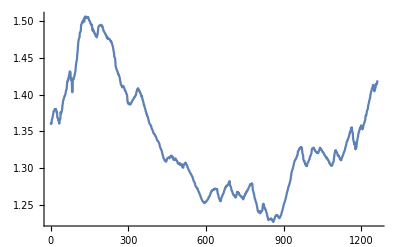

```mathematica
ListLinePlot[ds]
```

Trial some predictions based on existing mtca functions

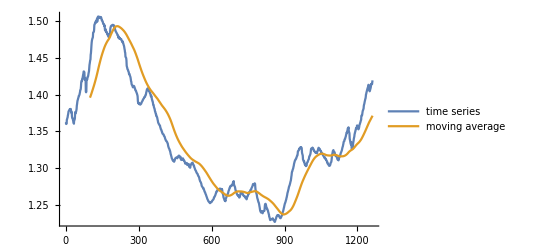

```mathematica
avg=MovingAverage[ds,100];
ListLinePlot[{ds,avg},PlotLegends->{"time series","moving average"}]
```

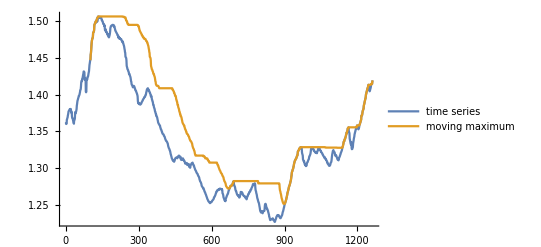

```mathematica
max=MovingMap[Max,ds,100];
ListLinePlot[{ds,max},PlotLegends->{"time series","moving maximum"}]
```

```mathematica
dsm=TimeSeriesModelFit[ds]
```

TimeSeriesModel[…]

Use TimeSeriesForecastpaclet:ref/TimeSeriesForecast to forecast the next 1000 values in the time series:

```mathematica
dsf=TimeSeriesForecast[dsm,{1000}];
```

Plot the time series along with the forecast:

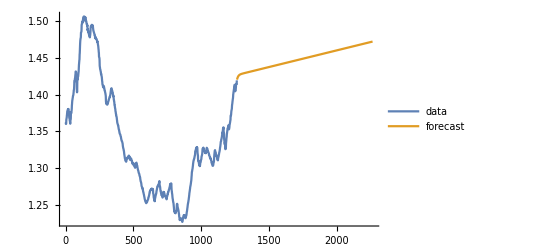

```mathematica
ListLinePlot[{ds,dsf},PlotLegends->{"data","forecast"}]
```

```mathematica
eproc=TimeSeriesModelFit[ds,{"SARIMA",12}]["Process"]
```

SARIMAProcess[-2.37682×10^-7,{0.41765,0.19998},1,{},{12,{-0.0917179},1,{-0.846865}},2.3812×10^-6]

```mathematica
forecast=TimeSeriesForecast[eproc,ds,{1000}];
```

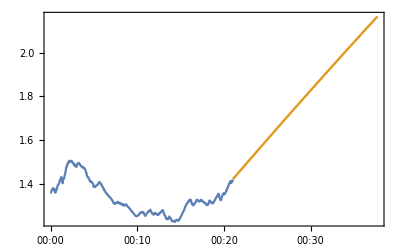

```mathematica
DateListPlot[{ds,forecast},Joined->True]
```

## Estimate the lag and embedding dimensions for the data

The lag is first estimated-

```mathematica
lag=RQAEstimateLag[ds]
```

305.726

However, a lag of 10 was used in previously published work (Ord&Hobbs, 2018; Ord et al., 2018) so that is what we will use here.

```mathematica
lag=10
```

10

The embedding dimension of the system is then estimated. The result below suggests a dimension of 3.

```mathematica
RQAEstimateDimensionality[ds,lag]
```

4.72984×10^-7

{Null,{{{2,0.40655,1262,4.72984×10^-8,1252,1.41325×10^-6},{3,0.0990338,1252,1.41325×10^-6,1242,2.94388×10^-6},{4,0.023539,1242,2.94388×10^-6,1232,4.36527×10^-6}}}}

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

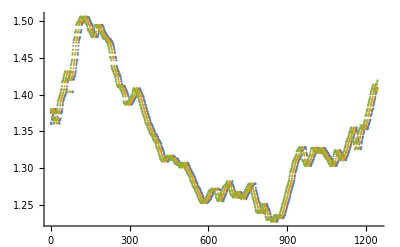

```mathematica
ListPlot[embedding]
```

## Plot the 3D spatial attractor

embedding is now a list of 3 columns of data, off set by the lag of 10, and we plot these in three dimensions, with the axes representing t, t+10, t+20

```mathematica
ParametricPlot3D[embedding[t],{t,1,650}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->{Orange,Specularity[White,10]},ViewPoint->{Left,Top}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->Directive[Green,Opacity[0.8],Specularity[White,20]],ViewPoint->{Left,Bottom}]
```

-Graphics3D-

## Interrogate the neighbours

These give you information on the neighbours, nearestneighbours and neighbours, but what is it you really need to know? Number of nearest neighbours? & don’t you normally (in VRA) search for these earlier while determining the dimensionality?

```mathematica
rn=RQANeighbors[embedding];
```

```mathematica
rnn=RQANearestNeighbors[embedding];
```

```mathematica
rnd=RQANeighborDistances[embedding];
```

## Calculate the distance map and the recurrence map

Webber (2012) numerical examples provide explicit step-by-step details on how input vectors (data) are delayed, embedded, normed, and rescaled
to define elements (distances) in the distance matrix (DM). Also described is how the recurrence matrix (RM) is derived from the DM by selecting only those recurrent points with distances falling within a selected RADIUS. Understanding of these simple examples should remove the mathematical mystery behind the basis of recurrence quantification analysis which simply finds patterns among recurrent points according to objective rules.
README_2012.PDF

Webber Chap 2.pdf the radius parameter implements a cut-off limit (Heavyside function) that transforms the distance matrix
(DM) into the recurrence matrix (RM). That is, all (i, j) elements in DM with distances at or below the RADIUS cutoff are included in the
recurrence matrix (element value = 1), but all other elements are excluded from RM (element value = 0). Note carefully that the RM
derives from the DM, but the two matrices are not identical.

FlipPhillips (pers.comm. 2019) Let us now look at the distance map. 1) recurrence maps are computed from distance maps.
2) distance maps are constant for any given embedding
3) recurrence maps are distance maps thresholded on a given distance
3a) If you don’t supply a threshold radius in the recurrence map command one will be computed for you (mean of all distances in the map)
4) ‘recurrence maps’ as created by your/my program a) use a strange distance measure that seems to be 100x the ‘real’ distance in Euclidean space and b) are a _combination_ of the distance map thresholded by the recurrence map.

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the distance map

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

The minimum and maximum are  determined to be 0 and 0.224875 - for rock4z
0 and 17251 for Rule30!

```mathematica
MinMax[dm]
```

{0.,0.224875}

find its dimensions

```mathematica
Dimensions[dm]
```

{1242,1242}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[dm]]
```

1242

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the recurrence map

```mathematica
Mean[Flatten[dm]]
```

0.0340171

So the automatic radius for Rule30 is 3462.13 while the automatic radius for rock4z is 0.0340171

```mathematica
rm=RQARecurrenceMap[embedding];
```

find its dimensions

```mathematica
Dimensions[rm]
```

{1242,1242}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[rm]]
```

1242

The recurrence map may be plotted

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

-Graphics-

The minimum and maximum of the recurrence are determined to be 0 and 1 respectively.

```mathematica
MinMax[rm]
```

{0,1}

## Calculate the RQA measures; compare with those using Webber’s RQA software

```mathematica
N[RQARecurrence[rm]]
```

0.680771

This compares with %REC=40.2 which is the result from Webber’s RQA for embedding dimension of 3 and a lag of 10

```mathematica
N[RQADeterminism[rm]]
```

0.999567

%DET=99.9 Result from RQA

```mathematica
N[RQALaminarity[rm,3]]
```

0.999178

%LAM=100 Result from RQA

```mathematica
N[RQATrappingTime[rm]]
```

220.737

TT=121.8 Result from RQA

```mathematica
N[RQATrend[rm]]
```

General::munfl: 0.00571231^619.5 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.102662^619.5 is too small to represent as a normalized machine number; precision may be lost.

-30.6973

Trend -56.4 Result from RQA

```mathematica
N[RQAEntropy[rm]]
```

8.02657

Entropy 7.6 Result from RQA

```mathematica
N[RQAChaos[rm]]
```

0.000805802

Result from RQA ? 1/DMAX

First pass code for calculating DMAX. It should be easy to derive from DET as only wanting the maximum of the length segments of the diagonal; don’t need to divide that number by the total number recurrent plots. You can change DMAX by changing the first part of the Range. For example, for @Range[500,w-1] DMAX=319, and for @Range[1000,w-1] DMAX=134

```mathematica
RQADmax[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

why has this stopped working? changed threshold to 3 - it worked. changed threshold to 2 - it worked. ? !

```mathematica
RQADmax[rm,2]//N
```

Total::tllen: Lists of unequal length in {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1191»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1190»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1189»},«45»,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1143»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1142»},«1191»} cannot be added.

Total::normal: Nonatomic expression expected at position 1 in Total[2].

segmentLengths[{1},2.]
 |  |  |  |

DMAX 1241 Result from RQA

1/DMax = ‘chaos’ as expected. ‘chaos’ is the maximum Lyapunov exponent. Note that the 2 here is the magnitude of the line required to be stated in the Webber code.

```mathematica
1/%
```

1/segmentLengths[{1},2.]
 |  |  |  |

=1/chaos - as expected

Similarly here for VMAX. The segment lengths are for the verticals.

```mathematica
RQAVmax[rm_,thresh_:2]:=Module[{ut,verts,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
verts=Transpose[ut];
segLens=segmentLengths[verts,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

```mathematica
RQAVmax[rm,2]
```

Total::normal: Nonatomic expression expected at position 1 in Total[2].

segmentLengths[{1},2]
 |  |  |  |

VMAX -592 Result from RQA

```mathematica
RQADetnew[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
nRP=Total[Flatten[ut]];
Total[lens]/nRP]/;SquareMatrixQ[rm]
```

```mathematica
RQADetnew[rm,2]//N
```

Total::tllen: Lists of unequal length in {{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1191»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1190»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1189»},«45»,{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1143»},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,«1142»},«1191»} cannot be added.

Total::normal: Nonatomic expression expected at position 1 in Total[2].

Total::normal: Nonatomic expression expected at position 1 in Total[2.].

Total::tllen: Lists of unequal length in {{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1191»},{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,«1190»},«48»,«1191»} cannot be added.

1.90605×10^-6 (Total[2.]+Total[{1}])
 |  |  |  |

```mathematica
RQARecurnew[rm_]:=Module[{ut,w,nMax,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
nMax=(w (w-1)/2);
nRP=Total[Flatten[ut]];
nRP/nMax]/;SquareMatrixQ[rm]
runLength[list_]:={First[#],Length[#]}&/@Split[list]
segmentLengths[m_,tLen_:2]:=Module[{rl,selFun,n},rl=runLength/@m;
selFun=Select[#[[1]]==1∧#[[2]]≥tLen&];
(selFun/@rl)/.{{}->{0},{1,n_}->n}]
```

```mathematica
RQARecurnew[rm]//N
```

0.680771

Marwan&Webber Equation 1.11

```mathematica
RQARatio=det/rec
```

det/rec

```mathematica
ListPlot[data]
```

-Graphics-

How do you choose the last number?

```mathematica
Manipulate[ListLinePlot[Take[data,{x,x+200}]],{{x,1},1,1200}]
```

```mathematica
ds["Properties"];
```

```mathematica
dsw=TimeSeriesWindow[ds,{1,1242}]
```

TimeSeries[…]

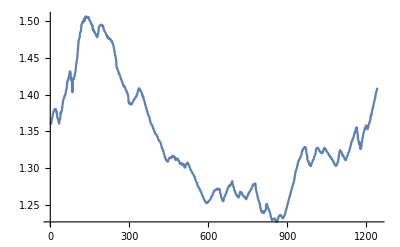

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All]
```

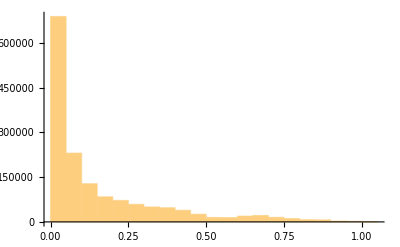

```mathematica
Histogram[Rescale[Flatten[dm]]]
```

```mathematica
Mean[Differences[ds["Times"]]]
```

1

CorrelationFunctionpaclet:ref/CorrelationFunction[data,hspec] estimates the correlation function at lags hspec from data.
hspec        | {τ_min,τ_max} | unit spaced from τ_min to τ_max

```mathematica
f=CorrelationFunction[ds,{1,1242}]
```

TimeSeries[…]

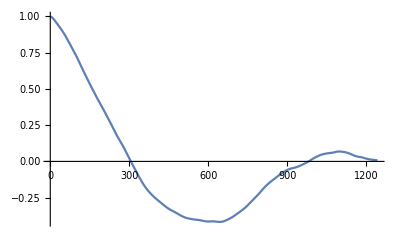

```mathematica
Plot[f[t],{t,1,1242},PlotRange->All]
```

```mathematica
FindRoot[f[t],{t,1}]
```

{t→305.726}

```mathematica
Fourier[data];
```

```mathematica
MinMax[Abs[Fourier[data]]]
```

{0.000064906,47.5676}

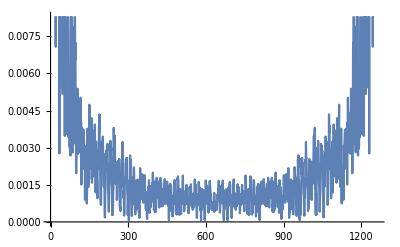

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->Automatic]
```

This is equivalent to the original estimate of the lag!

```mathematica
embedLag=RQAEstimateLag[ds]
```

305.726

```mathematica
RQAEstimateDimensionality[ds,embedLag]
```

4.72984×10^-7

{Null,{{{2,0.35251,1262,4.72984×10^-8,956,1.38088×10^-6},{3,0.0661538,956,1.38088×10^-6,650,2.69822×10^-6},{4,0.0116279,650,2.69822×10^-6,344,4.23066×10^-6}}}}

## Time Series Epochs start here

RQATimeSeriesEpochs[ts_,wid_,overlap_]:=
Table[TimeSeriesWindow[ts,{t0,t0+wid}],{t0,ts[“FirstTime”],ts[“LastTime”]-wid,overlap}]

```mathematica
e=RQATimeSeriesEpochs[dsw,200,50];
```

```mathematica
Head[%];
```

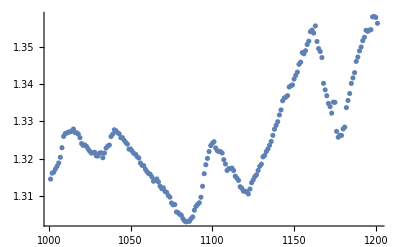

```mathematica
ListPlot[e[[-1]]]
```

If TimeSeriesEpochs defines the windows, how do you talk to the windows, compute the RQA, plot them?
6July2019 Getting there

So for each part of list e, calculate the following, with ds replaced by that part of the list:

```mathematica
embedding=RQAEmbed[e[[-1]],3,lag]
```

TimeSeries[…]

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
RQARecurrence[rm]//N
```

0.621731

```mathematica
RQADeterminism[rm]//N
```

0.997235

```mathematica
RQALaminarity[rm,3]//N
```

0.997334

```mathematica
RQATrappingTime[rm]//N
```

42.1375

```mathematica
RQATrend[rm]//N
```

-226.382

```mathematica
RQAEntropy[rm]//N
```

6.03963

```mathematica
RQAChaos[rm]//N
```

0.00555556

```mathematica
RQADmax[rm,2]//N
```

180.

```mathematica
RQAVmax[rm,2]//N
```

120.

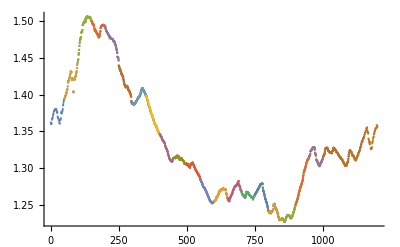
Map[-Graphics-]

```mathematica
Map[ListPlot[e]]
```

```mathematica
len=Length[e]
```

21

```mathematica
e[[3]]//N
```

TimeSeries[…]

```mathematica
Do[ListPlot[e[[i]]],{i,len}]
```

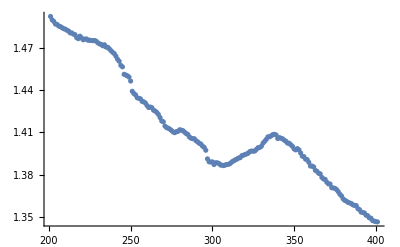

```mathematica
ListPlot[e[[5]]]
```

for each part of list e you need to calculate:
1. RQAEmbed[e[[part]],3,lag]
2. RQARecurrenceMap[RQAEmbed[e[[part]],3,lag]]
3. all the RQAs

copied from Flip Phillips epochs for alison.nb

```mathematica
eps=RQATimeSeriesEpochs[dsw,200,50];
```

So the following estimates the lag for each of the time series, eps 
Mappaclet:ref/Map[f,expr] or f/@expr   applies f to each element on the first level in expr.

```mathematica
Head[eps]
```

List

```mathematica
taus=Map[RQAEstimateLag,eps]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{68.1693,70.2085,69.0698,68.3119,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709}

```mathematica
Mean[%]
```

72.6888

RQAEmbed::usage=”RQAEmbed[ts,dims,tau] but why.”
#   Slot   represents the first argument supplied to a pure function. 
embeds as follows gives a list of TimeSeries, each of which it should be possible to address and plot separately.

```mathematica
embeds=Map[RQAEmbed[#,3,30.0]&,eps];
```

```mathematica
embeds=Map[RQAEmbed[#,3,10.0]&,eps];
```

```mathematica
Head[embeds]
```

List

N doesnt, and won’t, work here as it gives the numerical value of an expression, it does not count things.

```mathematica
N[embeds];
```

These bits of code successfully plot coloured squares for each epoch for the distance map

Mappaclet:ref/Map[f,expr] or f/@expr   applies f to each element on the first level in expr.

```mathematica
maps=RQADistanceMap/@embeds;
```

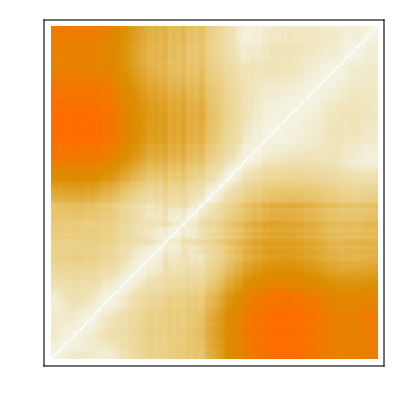
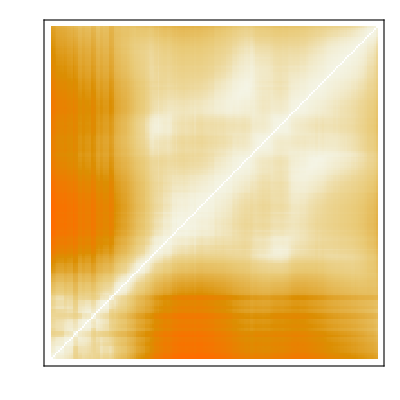
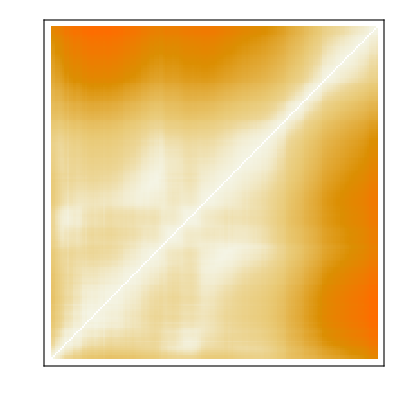
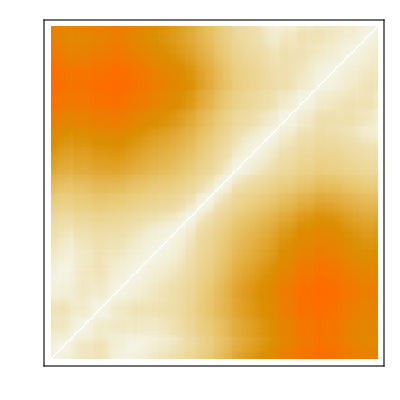
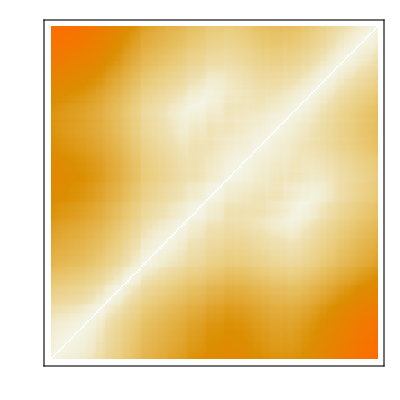
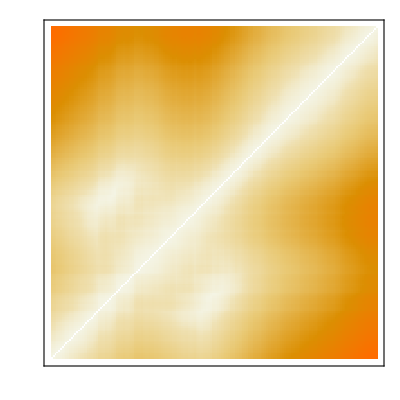
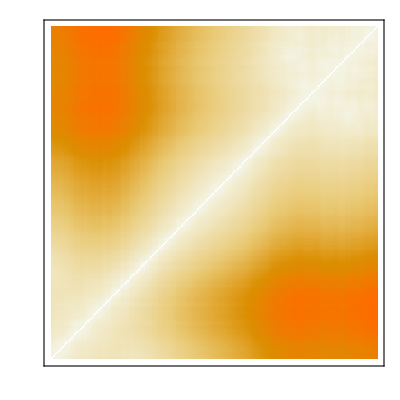
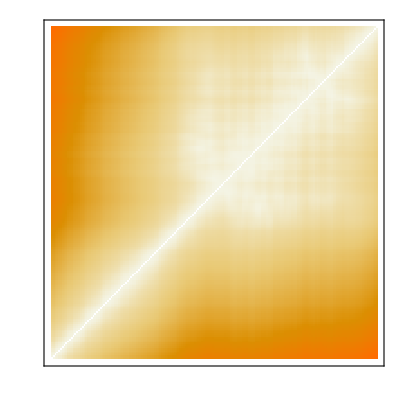

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None]&/@maps
```

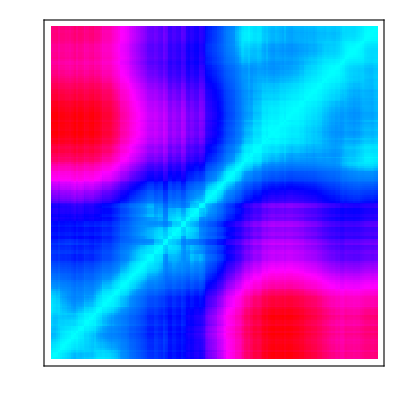
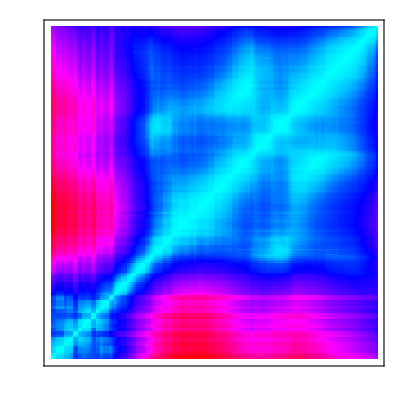
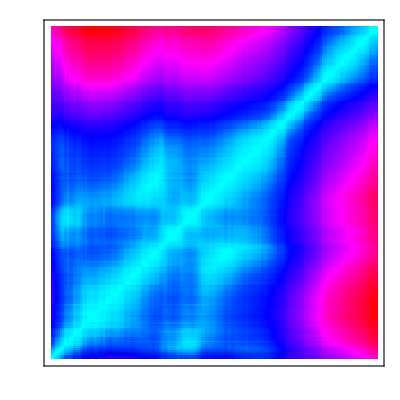
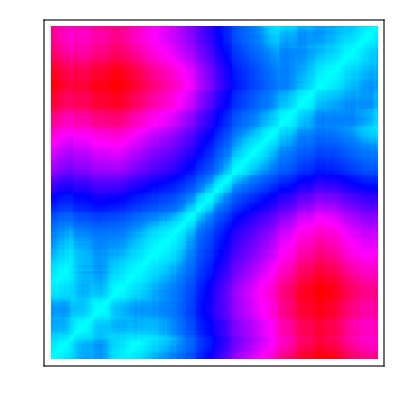
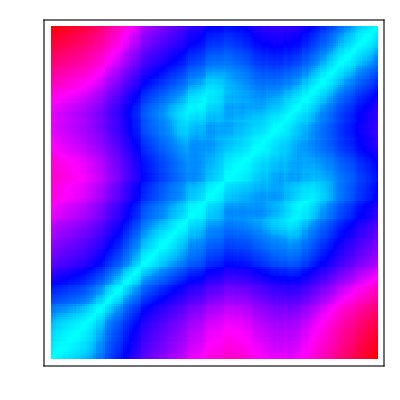
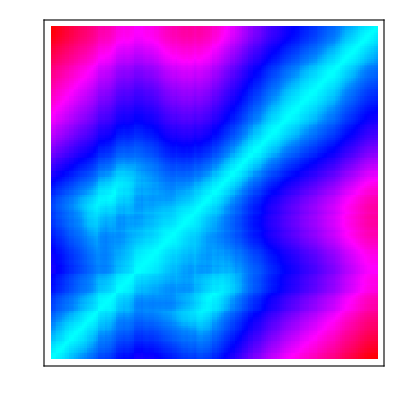
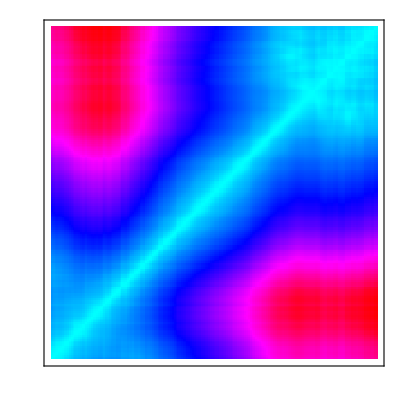
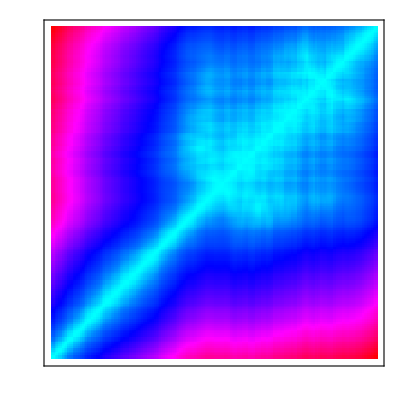
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@maps
```

```mathematica
(* numbers=RQARecurrenceMap[#,.01]&/@embeds; *)
```

```mathematica
numbers=RQARecurrenceMap[#]&/@embeds;
```

and for the recurrence map

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@numbers
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

I am still stuck with trying to obtain the RQA measures for each plot for each epoch - solved by Flip!  apply RQADeterminism etc. to numbers not to embeds

```mathematica
N[RQADeterminism/@numbers]
```

{0.997089,0.998308,0.999537,0.999479,0.99935,0.999239,0.998923,0.998896,0.999173,0.99938,0.999639,0.993113,0.990896,0.997122,0.998972,0.99916,0.999897,0.999606,0.99992,0.993206,0.997235}

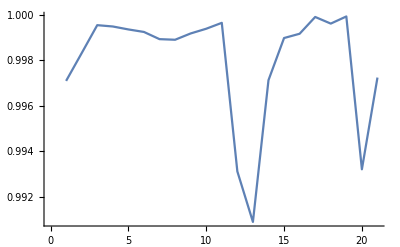

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQALaminarity/@numbers]
```

{0.997791,0.999342,0.999352,0.999792,0.999907,0.99981,0.999706,0.999908,0.999632,0.99969,0.99982,0.998253,0.997175,0.998015,0.999178,0.99944,0.999589,0.999901,0.99992,0.995223,0.998519}

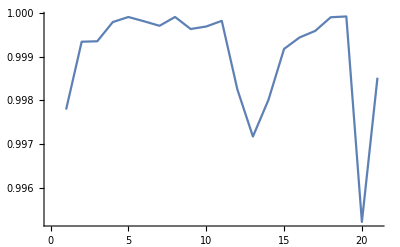

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQATrappingTime/@numbers]
```

{42.1144,51.3527,56.2135,52.1522,60.1173,53.6224,51.8325,60.7263,58.4839,53.1538,61.8939,27.5909,22.4741,45.4977,43.3973,42.332,50.6979,56.6983,69.4525,22.9779,42.1375}

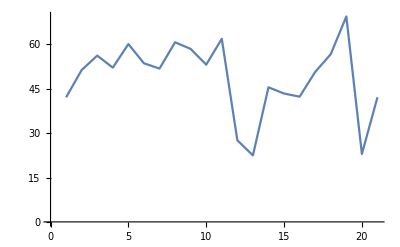

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQATrend/@numbers]
```

{-281.326,-209.771,-229.844,-303.475,-237.29,-255.829,-276.829,-233.432,-234.585,-295.594,-203.25,-138.922,-122.932,-228.663,-264.079,-229.398,-288.148,-265.237,-128.952,-140.051,-226.382}

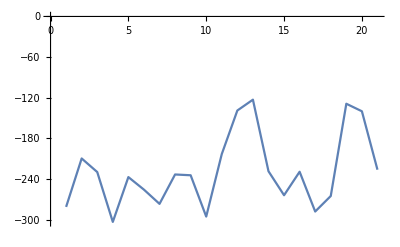

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQAEntropy/@numbers]
```

{5.92365,6.51639,6.82419,6.47836,6.6506,6.51049,6.51027,6.6544,6.68557,6.41888,6.61139,5.62574,5.25606,6.18024,6.2364,6.10935,6.53574,6.65041,6.96708,5.33634,6.03963}

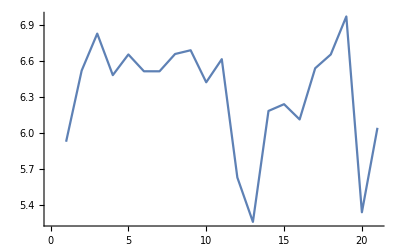

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQAChaos/@numbers]
```

{0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556}

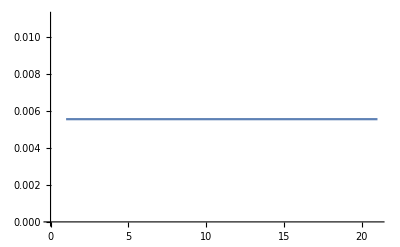

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQADmax/@numbers]
```

{180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.}

```mathematica
1/N[RQAChaos/@numbers]
```

{180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.,180.}

```mathematica
N[RQAVmax/@numbers]
```

{107.,143.,129.,97.,107.,103.,103.,117.,112.,105.,155.,111.,66.,122.,97.,144.,109.,121.,161.,157.,120.}

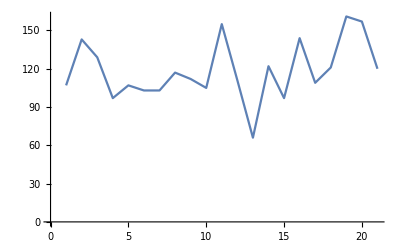

```mathematica
ListLinePlot[%]
```